```mathematica
Nt = 551; (*1000 -> default*)(*10 -> simple case to compare to reduced points*)
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*500 default from problem*)(*200 -> my choice*) (*25 -> simple case to compare to reduced points*)
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax);

(*For Eigenvalue Plots in Complex Plane*)
(*rs = {0.9,1,1.1};*)
(*rs = {1.4,1.5,1.6};*)(*When exporting RK4 and LD4*)

(*For Max Eigenvalue Plots*)
rs = Table[0.01*i,{i,1,200}];

maxevalsCN = Table[0,{i,1,Length[rs]}];
maxevalsEuler = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsRK4 = Table[0,{i,1,Length[rs]}];
maxevalsN = Table[0,{i,1,Length[rs]}];
```

```mathematica
Do[
deltat = deltax * rs[[p]];

T = Table[tn = ti + n *deltat, {n, 0, Nt}];
(*For Perodic Interpolation*) 
X = Table[xm = xi + m *deltax, {m, 0, Nx + 1}];
(*For Everything Else*)
X2 =  Table[xm = xi + m *deltax, {m, 0, Nx }];

f[x_] = Exp[-16* x^2];

L = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L = -1 * c * L ;
L//MatrixForm;

I1 = IdentityMatrix[Length[L]];


(* Crank-Nicolson *)
A = I1 - ((deltat / 2) * L);
B = I1 + ((deltat / 2) * L);
M = Inverse[A].B;

evals = Eigenvalues[N[M]];
realEvalsLD2 = Re[evals];
imagEvalsLD2 = Im[evals];

maxevalsCN[[p]] = Max[Abs[evals]];



(*Euler*)

Leuler = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
Leuler = -1 * c * Leuler ;

euler = I1 + deltat*Leuler;

evalsEuler = Eigenvalues[N[euler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];

maxevalsEuler[[p]] = Max[Abs[evalsEuler]];



(*RK2*)
LRK2 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LRK2 = -1 * c * LRK2 ;

LRK22 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LRK22//MatrixForm;

IRK2 = IdentityMatrix[Length[LRK2]];

Mrk = (IRK2 + (deltat * LRK2) + ((1/2)* (deltat^2) * (-c)^2 * LRK22));

evalsRK2 = Eigenvalues[N[Mrk]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];

maxevalsRK2[[p]] = Max[Abs[evalsRK2]];

(*RK4*)
LRK41 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK41//MatrixForm;

LRK42 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK42//MatrixForm;

LRK43 = (NDSolve`FiniteDifferenceDerivative[Derivative[3],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK43//MatrixForm;

LRK44 = (NDSolve`FiniteDifferenceDerivative[Derivative[4],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK44//MatrixForm;

IRK4 = IdentityMatrix[Length[LRK41]];

RK4X = Table[(-c)^i*(deltat)^i*ToExpression["LRK4"<>ToString[i]],{i,1,4}];

MRK4 = IRK4 + RK4X[[1]] + ((1/2) * (RK4X[[2]])) + ((1/6) * (RK4X[[3]])) + ((1/24) * (RK4X[[4]]));

evalsRK4 = Eigenvalues[N[MRK4]];

realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];

maxevalsRK4[[p]] = Max[Abs[evalsRK4]];

(*LD4*)
LN1 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LN1//MatrixForm;

LN2 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LN2//MatrixForm;

IN = IdentityMatrix[Length[LN1]];

NMX = Table[((-c)^i)*((deltat)^i)*ToExpression["LN"<>ToString[i]],{i,1,2}];

AN = IN - ((NMX[[1]] / 2)) + ((NMX[[2]]/12));
BN = IN + ((NMX[[1]] / 2) ) + ((NMX[[2]]/12));
MN = Inverse[AN].BN;

evalsLD4 = Eigenvalues[N[MN]];
realEvalsLD4 = Re[evalsLD4];
imagEvalsLD4 = Im[evalsLD4];

maxevalsN[[p]] = Max[Abs[evalsN]];


(*For Eigenvalue Plots in Complex Plane*)
(*exportData=Flatten/@Transpose[{realEvalsLD4, imagEvalsLD4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_circle_LD4_"<>ToString[rs[[p]]]<>".dat",exportData,"Table"];*)



,{p,1,Length[rs]}]

(*For Unit Circle*)
(* 
Nx = 200;
rsUnit = {1,10,20};

Do[
deltat = deltax * rsUnit[[p]];

(* Crank-Nicolson *)
A = I1 - ((deltat / 2) * L);
B = I1 + ((deltat / 2) * L);
M = Inverse[A].B;

evals = Eigenvalues[N[M]];
realEvals = Re[evals];
imagEvals = Im[evals];

maxevalsCN[[p]] = Max[Abs[evals]];

(*For Eigenvalue Plots in Complex Plane*)
exportData=Flatten/@Transpose[{realEvals, imagEvals}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_CN_"<>ToString[rsUnit[[p]]]<>".dat",exportData,"Table"];


,{p,1,Length[rsUnit]}]
*)



maxevalsCN = Join[{1},maxevalsCN];
rsCN = Join[{0},rs];

maxevalsEuler = Join[{1},maxevalsEuler];
rsEuler = Join[{0}, rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsRK4 = Join[{1},maxevalsRK4];
rsRK4 = Join[{0},rs];

maxevalsN = Join[{1},maxevalsN];
rsN = Join[{0},rs];

(*For Max Eigenvalue Plots*)
exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.631479,0.639878,-0.0677007,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«502»},{-0.246789,0.631479,0.639878,-0.0677007,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«502»},«47»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0431326,-0.246789,0.631479,«502»},«502»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.625917,0.646178,-0.0683028,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«502»},{-0.247156,0.625917,0.646178,-0.0683028,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«502»},«47»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0433639,-0.247156,0.625917,«502»},«502»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.620313,0.6525,-0.0689063,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«502»},{-0.2475,0.620313,0.6525,-0.0689063,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«502»},«47»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0435938,-0.2475,0.620313,«502»},«502»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

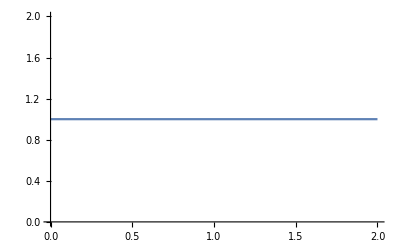

```mathematica
ListPlot[Transpose[{rsCN,maxevalsCN}], Joined->True]
```

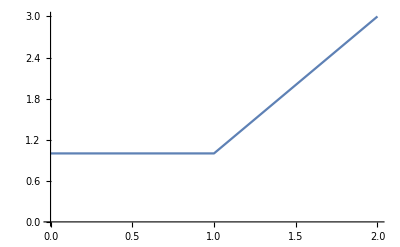

```mathematica
ListPlot[Transpose[{rsEuler,maxevalsEuler}],Joined->True]
```

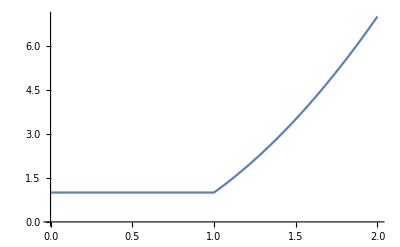

```mathematica
ListPlot[Transpose[{rsRK2,maxevalsRK2}],Joined->True]
```

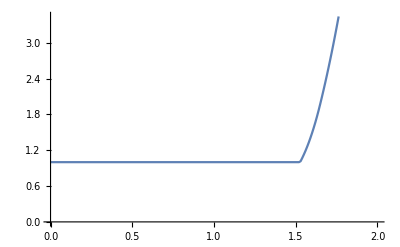

```mathematica
ListPlot[Transpose[{rsRK4,maxevalsRK4}],Joined->True]
```

```mathematica
ListPlot[Transpose[{rsN,maxevalsN}],Joined->True]
```

-Graphics-